```mathematica
ClearAll["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
n = 100;
```

```mathematica
randomSample = randomNumber[0,n];
```

```mathematica
sort = Sort[randomSample]
```

{0.469543,0.822487,0.990896,1.05585,1.28748,1.34167,1.44783,1.81261,1.82962,1.93468,1.98274,2.05404,2.0875,2.24656,2.31638,2.34078,2.34806,2.3853,2.46034,2.48245,2.52867,2.53806,2.6038,2.79065,2.79345,3.09729,3.11511,3.19209,3.21099,3.23982,3.35404,3.42569,3.46952,3.4996,3.50144,3.68716,3.74877,3.98595,4.12341,4.20158,4.27371,4.2777,4.28199,4.3141,4.33172,4.41221,4.4242,4.49442,4.49629,4.54144,4.58157,4.59162,4.61328,4.8192,4.87501,4.88883,4.97785,4.98727,5.00873,5.08278,5.21228,5.23506,5.35982,5.37534,5.40746,5.77671,5.80895,5.85454,5.96024,6.05553,6.21136,6.27015,6.28778,6.60234,6.74101,6.97543,7.11981,7.23953,7.29083,7.38418,7.46567,7.48378,7.50334,7.69491,7.75136,7.75418,7.89504,8.13948,8.20774,8.44136,8.80263,8.98296,9.02369,9.24968,9.56543,10.2405,10.6967,11.5864,12.4646,15.598}

```mathematica
μ = Mean[sort]
```

5.02794

```mathematica
s = StandardDeviation[sort]
```

2.76629

```mathematica
solA =NSolve[Integrate[x*E^(-a*x), {x, 0, ∞}] == μ, a, Reals][[1]][[1]][[2]]
```

0.445969

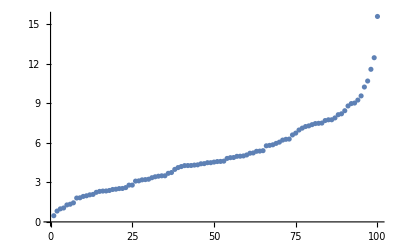

```mathematica
ListPlot[sort]
```

```mathematica
model1[x_] := E^(-solA*x)
```

```mathematica
solA2 =NSolve[Integrate[x*x*E^(-a*x), {x, 0, ∞}] == μ, a, Reals][[1]][[1]][[2]]
```

0.735439

```mathematica
Sqrt[Variance[sort]]
```

2.76629

```mathematica
pdf1[x_] := E^(-0.01*x)
```

```mathematica
pdf2[x_] := x*E^(-solA2*x)
```

```mathematica
pdf3[x_] := x*(x+0)*E^(-0*x)
```

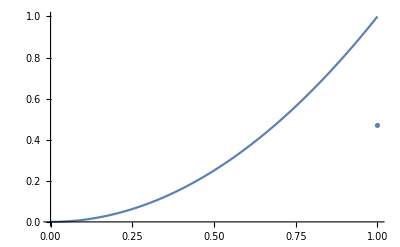

```mathematica
Show[Plot[pdf3[x], {x, 0, 1}], ListPlot[sort]]
```

```mathematica
(*NSolve[{Integrate[x^2 * x*(x+b)*E^(-a*x) - (x*x*(x+b)*E^(-a*x))^2, {x, 0, n}]== s^2, Integrate[(x+b)*x*x*E^(-a*x), {x, 0, n}] == μ}, {a,b}]*)
```

```mathematica
model1List = Table[model1[x_], {x, 1, n}];
```

```mathematica
Δ=1/n;
```

```mathematica
pData=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
xpData = Transpose[{sort, pData}];
```

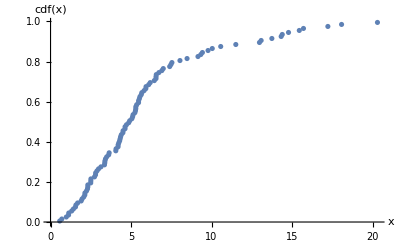

```mathematica
ListPlot[xpData, AxesLabel->{HoldForm[x], HoldForm[cdf[x]]}]
```

```mathematica
normDist = NormalDistribution[μ, s]
```

NormalDistribution[5.8374,4.8106]

```mathematica
pModel = CDF[normDist, sort]
```

{0.122139,0.124355,0.125739,0.131497,0.140527,0.144355,0.148348,0.148361,0.160228,0.166435,0.175798,0.178291,0.182343,0.185723,0.186991,0.192933,0.194783,0.200313,0.206941,0.206971,0.208888,0.211378,0.211591,0.211956,0.212659,0.217952,0.218974,0.222338,0.23067,0.231638,0.23665,0.239527,0.243587,0.268694,0.27322,0.27341,0.281468,0.287022,0.299207,0.309774,0.310551,0.312438,0.328058,0.332556,0.359273,0.376824,0.378157,0.383753,0.398566,0.411362,0.420651,0.422582,0.429775,0.441011,0.44301,0.465333,0.46915,0.478905,0.482188,0.488529,0.495856,0.5014,0.531361,0.540324,0.553293,0.556106,0.561502,0.575574,0.579152,0.593648,0.594061,0.636575,0.647093,0.649457,0.652091,0.665137,0.704963,0.720569,0.734612,0.774912,0.783254,0.786834,0.799303,0.816427,0.826611,0.828521,0.836004,0.895152,0.906354,0.936126,0.941698,0.942031,0.947936,0.954408,0.974289,0.981525,0.982308,0.985809,0.998957,0.999983}

```mathematica
comparedata = Transpose[{model1List, pData}];
```

Rule::rhs: Pattern x_ appears on the right-hand side of rule System`ProtoPlotDump`modelData[WrappedValues,{{2.71828^(-0.413895 x_),0.005},{2.71828^(-0.413895 x_),0.015},{2.71828^(-0.413895 x_),0.025},«46»,{2.71828^(-0.413895 x_),0.495},«50»},Charting`Private`Tag$129849]→{{2.71828^(-«20» x_),0.005},«49»,«50»}.

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

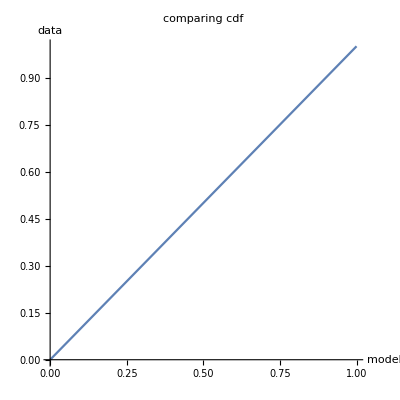

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```

```mathematica
m = xMean
```

xMean

```mathematica
s
```

s

```mathematica
1/n
```

1/50

```mathematica
1/50∑_(i=1)^n randomSample[[i]]
```

4.94036

```mathematica
solA =NSolve[Integrate[x*E^(-a*x), {x, 0, ∞}] == m, a, Reals][[1]][[1]][[2]]
```

ConditionalExpression[√(1/xMean),xMean>0]

```mathematica
solA
```

ConditionalExpression[√(1/xMean),xMean>0]

```mathematica
LogPlot[E^(-solA * x), {x, 0, n}]
```

-Graphics-

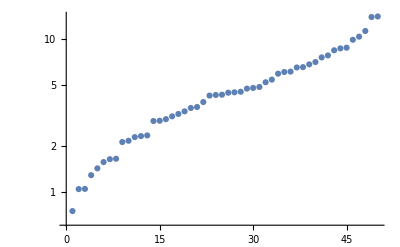

```mathematica
ListLogPlot[sort]
```

```mathematica
solA2 =NSolve[Integrate[x*x*E^(-a*x), {x, 0, ∞}] == m, a, Reals][[1]][[1]][[2]]
```

ConditionalExpression[Root[-2.+xMean #1^3&,1],xMean>0]

```mathematica
LogPlot[x*E^(-solA2 * x), {x, 0, n}]
```

-Graphics-

sigma2 = E[X^2] - mu^2 =
E[X^2] - integral(x * pdf(x) dx) =
integral(x^2 * λe^(-λx) dx) - integral(x * pdf(x) dx)^2 = σ^2

integral(x^2 * pdf(x) dx) - μ^2 =
integral(x^2 * pdf(x) dx) - (integral(x * pdf(x) dx)^2) = σ^2

```mathematica
pdf[x_] = x*(x+b)*E^(-a*x)
```

ⅇ^(-a x) x (b+x)

```mathematica
m
```

m

```mathematica
s
```

s

{}

ConditionalExpression[(6+2 a b)^2/a^8,Re[a]>0]

```mathematica
y = E^(-solA*x)
```

ConditionalExpression[ⅇ^(-x √(1/xMean)),xMean>0]

```mathematica
invModel2[v_]:=y;
invModel2[{x_,y_}]:={x,Log[y]}
```